# Examen parcial IV

## Pregunta 1

Para graficar el lado derecho, vemos que simplemente es una recta con pendiente diez que, al ser mod1, debe repetirse cada que su valor fuera a superar a uno:

```mathematica
f1[x_]:=10*x-Floor[10*x];
```

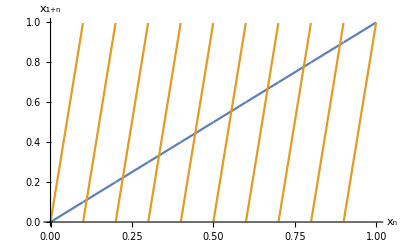

```mathematica
Plot[{x,f1[x]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

Tanto de la gráfica que acabamos de hacer como del efecto del módulo en los números en forma decimal, vemos que los puntos de equilibrio son  , es decir, .

Los ciclos corresponden a la repetición de un número racional con decimales periódicos. Un ejemplo fácil de ciclos de todos los períodos serían . Ahora, recordemos que los ciclos son puntos de equilibrio de los iterados de la ecuación, y su estabilidad depende de la estabilidad de estos puntos equilibrios de los iterados. Si la ecuación en diferencias recorre un lugar los dígitos de un número escrito en forma decimal, entonces el segundo iterado los recorre dos veces, el tercero tres veces, etc. De manera matemática, el -ésimo iterado está dado por . Recordemos que la estabilidad de un punto de equilibrio está dada por la derivada del lado derecho de la ecuación en el punto de equilibrio. En este caso, vemos que el -ésimo iterado consta simplemente de rectas , por lo que en cualquier punto, la derivada es igual a sus pendientes, que es , . En todos los casos, , por lo que son inestables.

Dado que los números irracionales tienen un número infinito de dígitos en forma decimal y no pueden ser periódicos, entonces todo número irracional en el intervalo [0,1) bajo esta ecuación necesariamente corresponde a una solución oscilatoria aperiódica. Como forman un conjunto no numerable, hay una infinidad de ellos.

El exponente de Lyapunov está dado por . Como discutimos en una pregunta anterior, la derivada del lado derecho de la ecuación en diferencias es siempre igual a 10 independientemente del valor de , puesto que son líneas rectas con la misma pendiente. Sustituyendo tenemos entonces que . Al ser un número positivo, sabemos que las soluciones con condiciones iniciales cercanas divergen exponencialmente, por lo que las soluciones en general son caóticas.

## Pregunta 2

Calculamos las soluciones de equilibrio resolviendo el sistema algebraico , :

```mathematica
Solve[{x==(r+1)*x-r*x^2-c*x*y,y==c*x*y},{x,y}]
```

{{x→1/c,y→((-1+c) r)/c^2},{x→0,y→0},{x→1,y→0}}

El equilibrio ,  es el equilibrio de extinción total porque indica la ausencia tanto de depredadores como presas, ,  es el equilibrio de extinción de depredadores porque sólo hay una cantidad positiva de presas, y ,  es el equilibrio de convivencia porque hay una cantidad positiva de ambos.

Primero calculamos la matriz jacobiana del sistema:

```mathematica
J1=({{D[(r+1)*x-r*x^2-c*x*y,x], D[(r+1)*x-r*x^2-c*x*y,y]}, {D[c*x*y,x], D[c*x*y,y]}})
```

{{1+r-2 r x-c y,-c x},{c y,c x}}

Y evaluamos primero en el equilibrio de extinción total y calculamos sus eigenvalores

```mathematica
MatrixForm[J1/.{x->0,y->0}]
```

(1+r | 0
0 | 0)

Es una matriz diagonal por lo que sus eigenvalores son  y . Vemos que siempre se cuemple que , pero en el segundo caso obtenemos  que se cumple cuando , es decir, la condición de estabilidad del estado de extinción es .
Ahora evaluamos el equilibrio de extinción de depredadores y calculamos sus eigenvalores

```mathematica
MatrixForm[J1/.{x->1,y->0}]
```

(1-r | -c
0 | c)

```mathematica
Eigenvalues[{{1-r,-c},{0,c}}]
```

{c,1-r}

En este caso los eigenvalores son  y , por lo que obtenemos los siguientes criterios de estabilidad:  y  es decir, .
Por último, evaluamos en el equilibrio de convivencia y calculamos el polinomio característico

```mathematica
FullSimplify[MatrixForm[J1/.{x->1/c,y->((-1+c) r)/c^2}]]
```

(1-r/c | -1
((-1+c) r)/c | 1)

```mathematica
Collect[CharacteristicPolynomial[{{1-r/c,-1},{((-1+c) r)/c,1}},x],x]
```

1+r-(2 r)/c+(-2+r/c) x+x^2

Y el criterio de Jury dicta que , y sustituyendo obtenemos . Dividimos esta desigualdad doble en tres desigualdades de la siguiente manera: desigualdad 1


 (porque  es un parámetro positivo)
 (porque  también es positivo)

Desigualdad 2





Desigualdad 3






Las desigualdades 1 y 3 pueden escribirse como la desigualdad doble

El límite superior del valor de  para la estabilidad del equilibrio de convivencia es , por lo que examinamos las soluciones un poco antes y después de este valor, fijando . Antes de la bifurcación obtenemos:

```mathematica
{x->1/c,y->((-1+c) r)/c^2}/.{r->3.1,c->1.8}
```

{x→0.555556,y→0.765432}

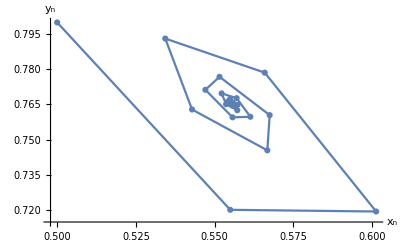

```mathematica
solantes=RecurrenceTable[{x[n+1]==(3.1+1)*x[n]-3.1*x[n]^2-1.8*x[n]*y[n],y[n+1]==1.8*x[n]*y[n],x[1]==0.5,y[1]==0.8},{x,y},{n,50}];
ListPlot[solantes,Joined->True,Mesh->All,AxesLabel->{Subscript[x,n],Subscript[y,n]},PlotRange->All]
```

La solución oscila y tiende al punto de equilibrio, puesto que en este rango el estado de convivencia es estable. Ahora observamos el comportamiento después de la bifurcación:

```mathematica
{x->1/c,y->((-1+c) r)/c^2}/.{r->3.1,c->2.2}
```

{x→0.454545,y→0.768595}

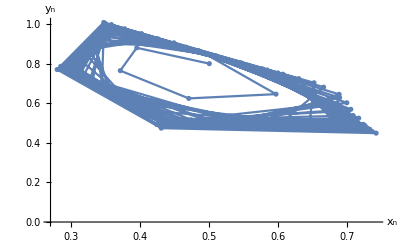

```mathematica
soldespues=RecurrenceTable[{x[n+1]==(3.1+1)*x[n]-3.1*x[n]^2-2.2*x[n]*y[n],y[n+1]==2.2*x[n]*y[n],x[1]==0.5,y[1]==0.8},{x,y},{n,150}];
ListPlot[soldespues,Joined->True,Mesh->All,AxesLabel->{Subscript[x,n],Subscript[y,n]},PlotRange->All]
```

Vemos que la solución ya no es atraída por el punto de equilibrio sino que ahora es repelida por éste y atraída por un ciclo límite estable. Entonces, la bifurcación consiste en un punto de equilibrio estable, que se vuelve inestable y surje un ciclo límite estable. Esto corresponde a una bifurcación de Hopf supercrítica.

## Pregunta 3

Sea

Calcula la estabilidad del punto de equilibrio , y demuestra que existe una bifurcación de flip en .

Para la estabilidad, calculamos la derivada







Vemos que hay pérdida de estabilidad del punto de equilibrio en . Para saber que la bifurcación es de flip, tenemos que ver que la derivada es negativa y disminuye de mayor a -1 a menor a -1. Entonces vemos cómo es la derivada para números positivos:



Por lo tanto, cuando , la derivada es menor a -1 y el punto de equlibrio es inestable, y cuando  (pero cerca de cero), la derivada es negativa pero mayor a -1 por lo que es estable, y hay una bifurcación de flip.

Usando la serie de Taylor del segundo iterado hasta orden tres, muestra que hay un ciclo límite de periodo dos para , que coalesce con el punto de equilibrio en . Argumenta porqué esto indica que hay una bifurcación de flip subcrítica.

Definimos el lado derecho de la ecuación:

```mathematica
f[x_,r_]:=-(1+r)*x-x^2-2*x^3;
```

Y expandimos su segundo iterado hasta tercer orden:

```mathematica
Series[f[f[x,r],r],{x,0,3}]
```

(-1-r)^2 x+(-r-r^2) x^2+2 (1+3 r+3 r^2+r^3) x^3+O[x]^4

Calculamos las soluciones de equilibrio del segundo iterado como

```mathematica
Solve[x==(-1-r)^2 x+(-r-r^2) x^2+2 (1+3 r+3 r^2+r^3) x^3,x]
```

{{x→0},{x→(r+r^2-√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))},{x→(r+r^2+√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3))}}

Obtenemos el punto de equilibrio orignal, más otros dos puntos de equilibrio que corresponden al ciclo de período dos. Podemos ver que, cuando , estas soluciones son complejas, por lo que sólo existen cuando . Cuando , vemos que ambos puntos del ciclo coinciden con la solución de equilibrio, puesto que todo está muliplicado por  en el numerador. Mostramos anteriormente que cuando  el punto de equilibrio es estable. Como en este régimen existe el ciclo, concluimos que debe ser de flip subcrítico (en las bifucarciones supercríticas, el ciclo existe cuando el punto de equilibrio es inestable, y en el caso subcrítico, el ciclo existe cuando el punto de equilibrio es estable). 
Opcionalmente podemos obtener el diagrama de bifurcación y examinar las soluciones numéricas para comprobar que el ciclo es inestable:
En la aproximación:

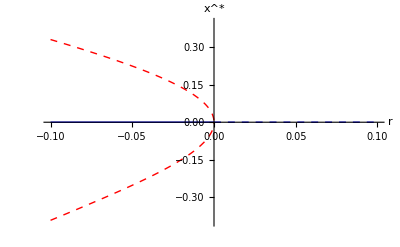

```mathematica
Show[{Plot[0,{x,-0.1,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-0.1,0.1},{-0.4,0.4}}],Plot[0,{x,0,0.1},PlotStyle->{Blue,Thick,Dashed}],Plot[(r+r^2-√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3)),{r,-0.1,0},PlotStyle->{Red,Thick,Dashed}],Plot[(r+r^2+√(-16 r-55 r^2-70 r^3-39 r^4-8 r^5))/(4 (1+3 r+3 r^2+r^3)),{r,-0.1,0},PlotStyle->{Red,Thick,Dashed}]}]
```

En el sistema no lineal completo:

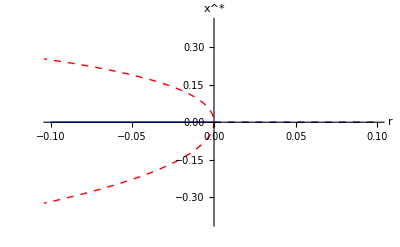

```mathematica
cyc1=ParallelTable[{r,x/.FindRoot[x==f[f[x,r],r],{x,1}]},{r,-1,0,0.0001}];
cyc2=ParallelTable[{r,x/.FindRoot[x==f[f[x,r],r],{x,-1}]},{r,-1,0,0.0001}];
Show[{Plot[0,{x,-0.1,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-0.1,0.1},{-0.4,0.4}}],Plot[0,{x,0,0.1},PlotStyle->{Blue,Thick,Dashed}],ListPlot[cyc1,Joined->True,PlotStyle->{Red,Thick,Dashed}],ListPlot[cyc2,Joined->True,PlotStyle->{Red,Thick,Dashed}]}]
```

Una solución después de la bifurcación:

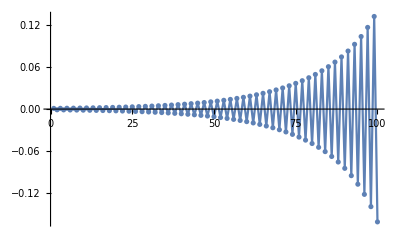

```mathematica
sol2=RecurrenceTable[{x[n+1]==f[x[n],0.05],x[1]==0.001},x,{n,1,100}];
ListPlot[sol2,Joined->True,Mesh->All,PlotRange->All]
```

Una solución antes de la bifurcación dentro del ciclo inestable:

```mathematica
cyc1[[9500]]
```

{-0.0501,0.189383}

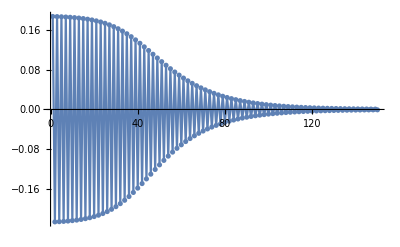

```mathematica
sol3=RecurrenceTable[{x[n+1]==f[x[n],-0.05],x[1]==0.188},x,{n,1,150}];
ListPlot[sol3,Joined->True,Mesh->All,PlotRange->All]
```

Una solución antes de la bifurcación fuera del ciclo inestable:

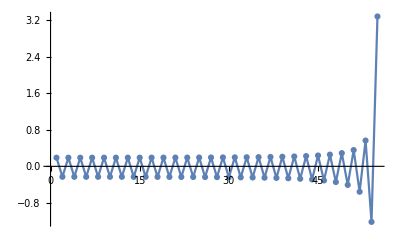

```mathematica
sol4=RecurrenceTable[{x[n+1]==f[x[n],-0.05],x[1]==0.1895},x,{n,1,55}];
ListPlot[sol4,Joined->True,Mesh->All,PlotRange->All]
```